# 1.1 Elementary functions

```mathematica
f[x_]=Cosh[x];
g[x_]=Cosh[2x];
h[x_]=x^2;

Plot[{f[x],g[x],h[x]},{x,-1,1},PlotLabels->"Expressions"]
Series[f[x],{x,0,5}]
Series[g[x],{x,0,5}]
f[0]
g[0]
```

-Graphics-

1+x^2/2+x^4/24+O[x]^6

1+2 x^2+(2 x^4)/3+O[x]^6

1

1

## 5

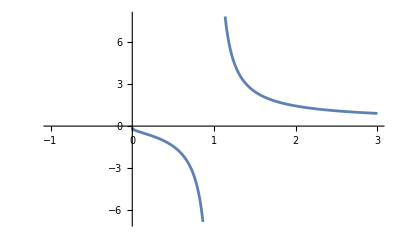

```mathematica
Plot[1/Log[x],{x,-1,3}]
```

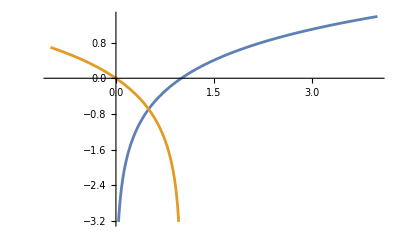

```mathematica
Plot[{Log[x],Log[1-x]},{x,-1,4}]
```

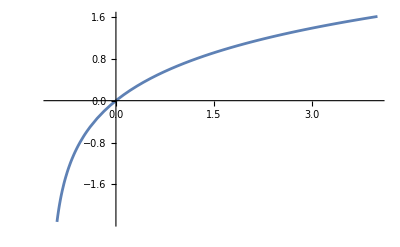

```mathematica
Plot[Log[x+1],{x,-1,4}]
```

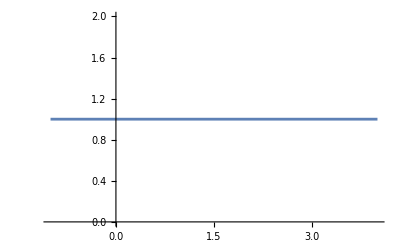

```mathematica
Plot[Log[Exp[1]],{x,-1,4}]
```

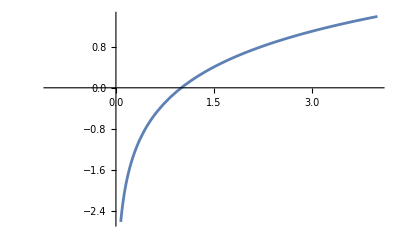

```mathematica
Plot[Log[x],{x,-1,4}]
```

```mathematica
Log[Exp[1]]
```

1

```mathematica
N[Exp[1],4]
```

2.718

^Euler’s number.

```mathematica
Log[2.718]
```

0.999896

```mathematica
Log[1]
```

0

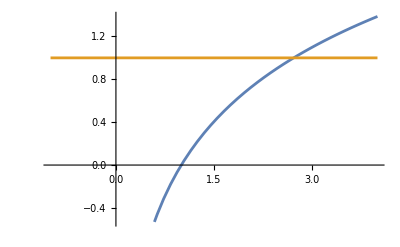

```mathematica
Plot[{Log[x],Exp[0]},{x,-1,4}]
```

```mathematica
Plot[{Log[x],1},{x,-1,4}]
```

-Graphics-

```mathematica
Exp[Log[1]]
```

1

```mathematica
Log[Exp[1]]
```

1

```mathematica
Log[Exp[5]]
```

5

```mathematica
Exp[Log[5]]
```

5

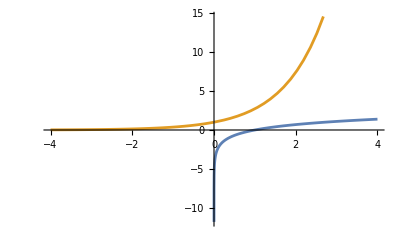

```mathematica
Plot[{Log[x],Exp[x]},{x,-4,4}]
```

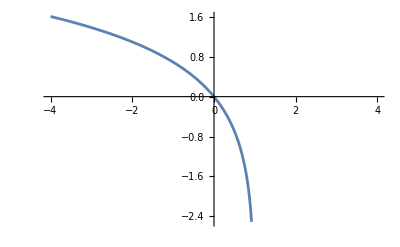

```mathematica
Plot[Log[1-x],{x,-4,4}]
```

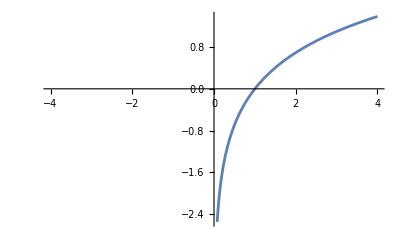

```mathematica
Plot[Log[x],{x,-4,4}]
```

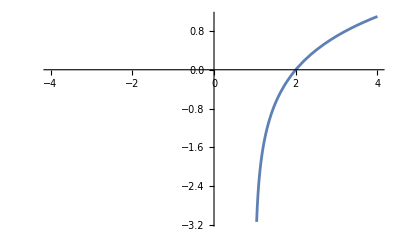

```mathematica
Plot[Log[x-1],{x,-4,4}]
```

```mathematica
Plot[Log[1-x],{x,-4,4}]
```

-Graphics-

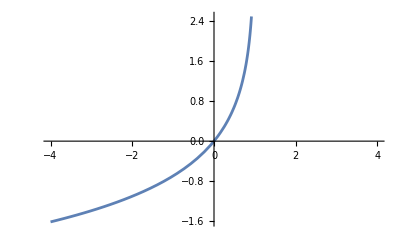

```mathematica
Plot[-Log[1-x],{x,-4,4}]
```

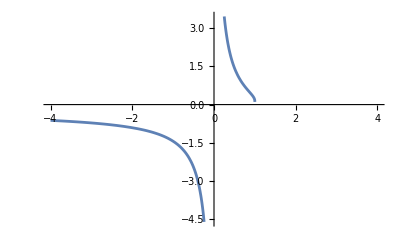

```mathematica
Plot[-1/Log[1-x],{x,-4,4}]
```

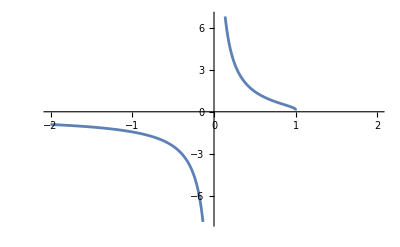

```mathematica
Plot[-1/Log[1-x],{x,-2,2}]
```

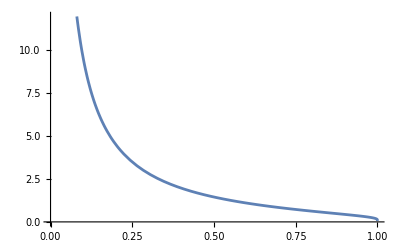

```mathematica
Plot[-1/Log[1-x],{x,0,1}]
```

## 6

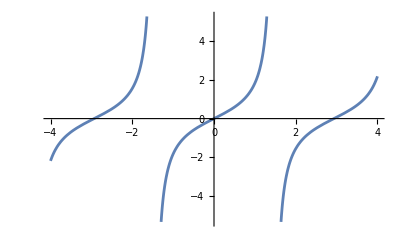

```mathematica
Plot[Tan[1/2(π*x-x)],{x,-4,4}]
```

## 7

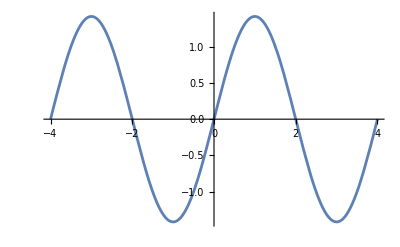

```mathematica
f[x_]=√2*Sin[(π*x)/2];
Plot[f[x],{x,-4,4}]
```

```mathematica
Plot[{f[x]},{x,-4,4}]
```

-Graphics-

```mathematica
Sin[0]
```

0

```mathematica
Sin[π]
```

0

```mathematica
Sin[1]
```

Sin[1]

```mathematica
N[Sin[π/2],4]
```

1.

Mathematica will always default to radians when calling trig functions?

```mathematica
Cos[0]
```

1

```mathematica
Cos[π/2]
```

0

```mathematica
Sin[0]
```

0

## 8

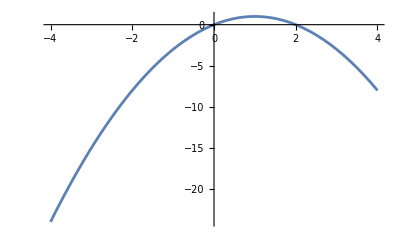

```mathematica
Plot[-x^2+2x,{x,-4,4}]
```

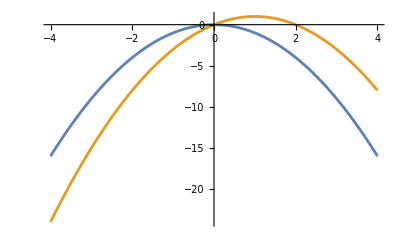

```mathematica
Plot[{-x^2,-x^2+2x},{x,-4,4}]
```

## 9

```mathematica
N[Exp[1]^4,4]
2.718^4
```

54.6

54.5755

```mathematica
Sinh[2]/4
```

Sinh[2]/4

```mathematica
N[Sinh[2],4]
```

3.627